```mathematica
ClearAll["Global`*"];
```

```mathematica
x1 = 0; x2=10;hmem=1;tb=5;μ=0; ϕ=0;
hpStep[t_, tb_]:=hmem HeavisideTheta[t-tb]
hpTanh[t_, tb_, scale_]:=hmem Tanh[scale(t-tb)]/2 + 1/2
```

```mathematica
Sstep[t_]:= 1/2 hmem(1+μ)(t-tb)HeavisideTheta[t-tb]Cos[2 ϕ]
STanh[t_, scale_]:= 1/2 hmem(1+μ)(Log[Cosh[scale(t-tb)]]/(2 scale) + (t-tb)/2)Cos[2 ϕ]
```

```mathematica
hpSacle[scale_] :=Plot[{hpStep[x, tb], hpTanh[x, tb,scale]}, {x, 0, 10}]
```

```mathematica
Manipulate[hpSacle[n], {n, 1,20}]
```

```mathematica
Resd[scale_] := Plot[{Sstep[x], STanh[x, scale]}, {x, 0, 10}]
```

```mathematica
Manipulate[Resd[n], {n, 1,20}]
```

```mathematica
generateTanhdata[scale_]:=STanh[#, scale]& /@ Range[0, 10, 0.05]
```

```mathematica
scale=1;
dataStep=Transpose@{Range[0, 10, 0.05],Map[Sstep, Range[0, 10, 0.05]]};
dataTanh=Transpose@{Range[0, 10, 0.05],generateTanhdata[scale]};
```

```mathematica
parabolaStep=Fit[dataStep,{1,x,x^2},x];
parabolaTanh=Fit[dataTanh,{1,x,x^2},x];
```

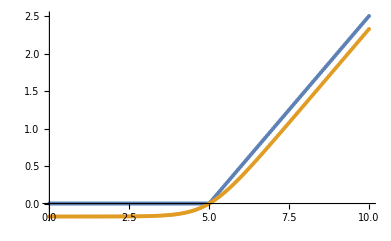

```mathematica
ListPlot[{dataStep,dataTanh }]
```

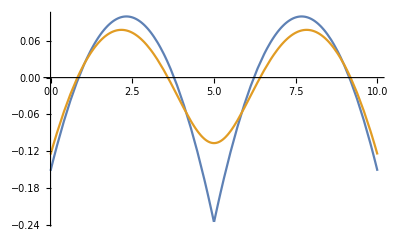

```mathematica
Plot[{Sstep[ x]-parabolaStep,STanh[x, scale]- parabolaTanh}, {x, 0, 10}]
```

```mathematica
FTStep[ω]=Simplify[FourierTransform[Sstep[ x]-parabolaStep, x,ω ]Conjugate[FourierTransform[Sstep[ x]-parabolaStep, x,ω ]]//ComplexExpand];
```

```mathematica
(*FTTanh[ω ]=Simplify[FourierTransform[STanh[x]- parabolaTanh, x,ω ]Conjugate[FourierTransform[STanh[x]- parabolaTanh, x,ω ]]//ComplexExpand];*)
```

```mathematica
Stepdata = Table[{x,Sstep[ x]-parabolaStep}, {x, Range[0, 10, 0.05]}];
Tanhdata = Table[{x,STanh[x, scale]- parabolaTanh}, {x, Range[0, 10, 0.05]}];
```

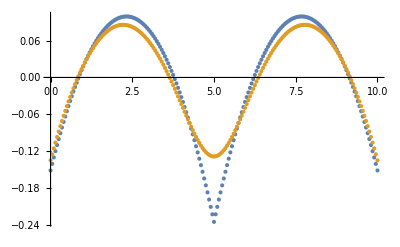

```mathematica
ListPlot[{Stepdata, Tanhdata}]
```

```mathematica
Extract[Stepdata, {All,2}];
```

```mathematica
dctStep =FourierDCT[Extract[Stepdata, {All,2}]];
dctTanh =FourierDCT[Extract[Tanhdata, {All,2}]];
```

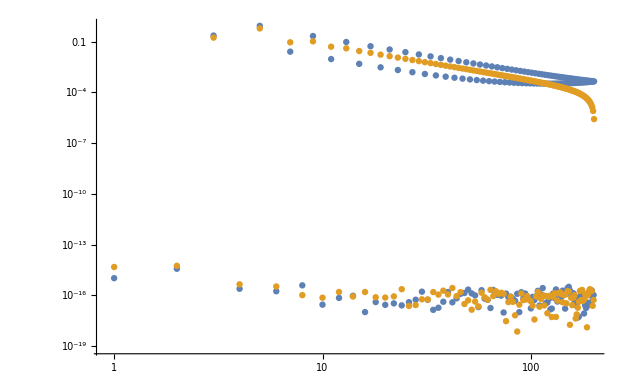

```mathematica
ListLogLogPlot[{Abs[dctStep], Abs[dctTanh]}, PlotRange->All]
```

```mathematica
(*Generate fourier tranform*)
```

```mathematica
f1[x_]:= Piecewise[{{Abs[Sin[2 π x/10]]-0.5, 0≤x≤10}},0]
f2[x_, scale_]:= Piecewise[{{scale(Sin[2 π x/6-0.5]), 0≤x≤10}},0]
```

```mathematica
fPlot[scale_]:=Plot[{f1[x], f2[x, scale]}, {x, -5 ,15}]
```

```mathematica
Manipulate[fPlot[k], {k, 0.3, 0.45}]
```

```mathematica
scalefactor = 0.2;
```

```mathematica
FT1[ω]=Simplify[FourierTransform[f1[x], x,ω ]Conjugate[FourierTransform[f1[x], x,ω ]]//ComplexExpand];
FT2[ω]=Simplify[FourierTransform[f2[x, scalefactor ], x,ω ]Conjugate[FourierTransform[f2[x, scalefactor ], x,ω ]]//ComplexExpand];
```

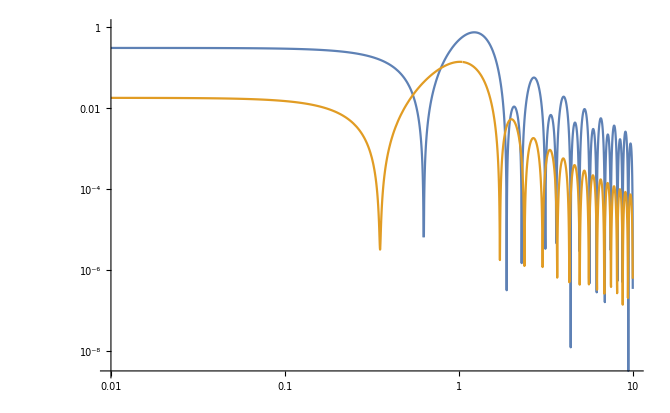

```mathematica
LogLogPlot[ {Abs[FT1[ω]], Abs[FT2[ω]]}, {ω, 0.01,10}]
```